# “Good” Semicomplete Digraphs

Function goodSemiCompleteD[n,m] generates a random semicomplete digraph free of all forbidden structures within five vertices. Hence the output is most likely a desired semicomplete digraphs free of forbidden minors, but some bad cases occur too, see example 3.

```mathematica
<<PolyhedralComb`
```

## Example 1

```mathematica
d=goodSemiCompleteD[8,6]
```

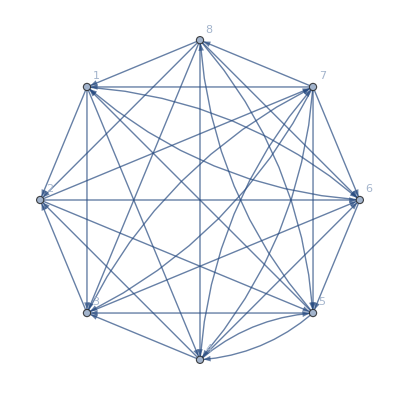
```mathematica
d=-Graphics-
```

-Graphics-

```mathematica
bfsVPartition[d,#]&/@maxOutDegreeVS@d
```

{{{{7},{}},{{4,3,2},{}},{{1,5,8},{{5->8,8->5}}},{{6},{}}},{{{8},{}},{{7,5},{}},{{4,3,2,6},{}},{{1},{}}}}

```mathematica
CyclePacking={{4,7},{5,8},{1,6}}
```

{{4,7},{5,8},{1,6}}

```mathematica
FeedbackVS={5,6,7}
```

{5,6,7}

```mathematica
d//AcyclicGraphQ[Subgraph[#,Complement[VertexList[#],FeedbackVS]]]&
```

True

```mathematica
fig1=LayeredGraphPlot[{1->2,1->3,1->4,5->4,4->5,5->3,6->1,4->7,8->2,8->3,8->4,5->8,8->5,1->6,6->5,7->4,3->7,7->3,2->7},VertexLabeling->True,MultiedgeStyle->All,VertexCoordinateRules->{{1,1},{1,2},{0,2},{-1,2},{-1,1},{0,0},{0,3},{0,1}}];
fig2=LayeredGraphPlot[{1->2,1->3,1->4,2->5,1->6,6->1,2->7,3->7,7->3,4->7,7->4,6->5,5->8,8->5,7->8,4->5,5->4},VertexLabeling->True,MultiedgeStyle->All,VertexCoordinateRules->{{0,-1},{0.5,0},{-0.5,0},{-1.5,0},{0.5,1},{1.5,0},{-0.5,1},{0,2}}];
```

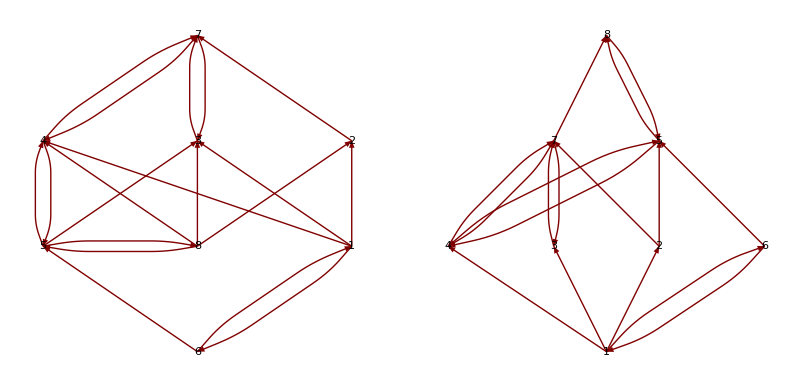

```mathematica
GraphicsRow[{fig1,fig2},ImageSize->Full]
```

### Example 2

```mathematica
d=goodSemiCompleteD[7,6]
```

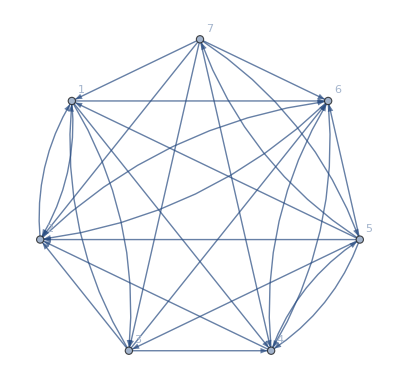
```mathematica
d=-Graphics-
```

-Graphics-

```mathematica
bfsVPartition[d,#]&/@maxOutDegreeVS@d
```

{{{{5},{}},{{7,4},{}},{{1,3,6},{{1->3,3->1}}},{{2},{}}},{{{7},{}},{{5},{}},{{4},{}},{{1,3,6},{{1->3,3->1}}},{{2},{}}}}

```mathematica
CyclePacking={{5,7},{4,6},{1,2}};
```

```mathematica
FeedbackVS={1,5,6};
```

```mathematica
d//AcyclicGraphQ[Subgraph[#,Complement[VertexList[#],FeedbackVS]]]&
```

True

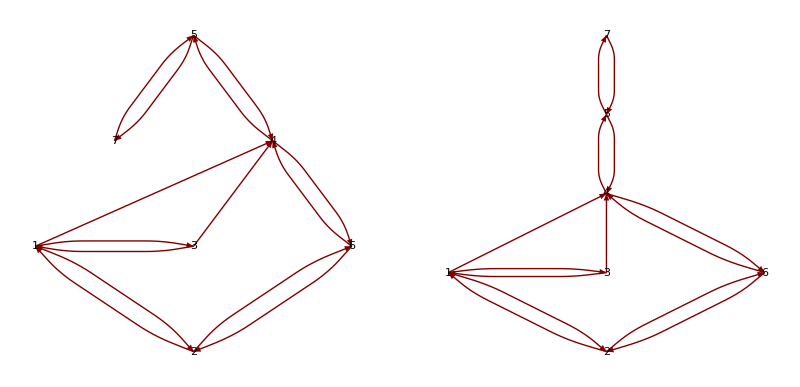

```mathematica
fig1=LayeredGraphPlot[{5->7,7->5,5->4,4->5,1->4,3->4,1->3,3->1,4->6,6->4,1->2,2->1,2->6,6->2},VertexLabeling->True,MultiedgeStyle->All,VertexCoordinateRules->{{0,3},{-0.5,2},{0.5,2},{-1,1},{0,1},{1,1},{0,0}}];
fig2=LayeredGraphPlot[{7->5,5->7,5->4,4->5,1->4,3->4,1->3,3->1,4->6,6->4,1->2,2->1,2->6,6->2},VertexLabeling->True,MultiedgeStyle->All,VertexCoordinateRules->{{0,4},{0,3},{0,2},{-1,1},{0,1},{1,1},{0,0}}];
GraphicsRow[{fig1,fig2},ImageSize->Full]
```

## Example 3(bad one)

This digraph turns out not to be a good one, since it has a 5-Ring, which can simply be obtained by contracting vertex 4.

```mathematica
d=goodSemiCompleteD[7,6]
```

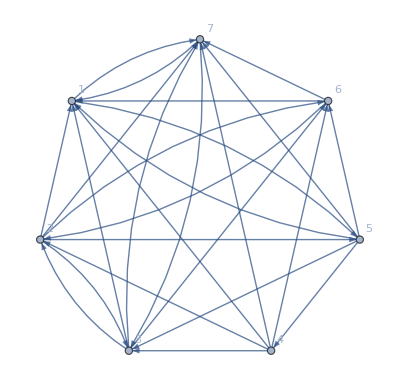
```mathematica
d=-Graphics-
```

-Graphics-

```mathematica
bfsVPartition[d,#]&/@maxOutDegreeVS@d
```

{{{{2},{}},{{4,3,6},{}},{{5,7},{}},{{1},{}}},{{{4},{}},{{5},{}},{{2,1},{}},{{3,6,7},{{3->7,7->3},{3->6,6->7,7->3}}}},{{{5},{}},{{2,1},{}},{{3,4,6,7},{{3->7,7->3},{3->6,6->7,7->3}}}}}

```mathematica
CyclePacking={{1,5},{2,6},{3,7}}
```

{{1,5},{2,6},{3,7}}

```mathematica
FeedbackVS={1,2,7}
```

{1,2,7}

```mathematica
d//AcyclicGraphQ[Subgraph[#,Complement[VertexList[#],FeedbackVS]]]&
```

True

```mathematica
fig1=LayeredGraphPlot[{4->2,2->3,3->2,2->6,6->2,5->4,5->3,5->6,3->7,7->3,1->5,5->1,1->7,7->1},VertexLabeling->True,MultiedgeStyle->All,VertexCoordinateRules->{{-1.5,2},{0,3},{0,2},{1.5,2},{-0.5,1},{0.5,1},{0,0}}];
fig2=LayeredGraphPlot[{5->4,2->5,1->5,5->1,2->3,3->2,2->6,6->2,3->1,6->1,1->7,7->1,3->7,7->3},VertexLabeling->True,MultiedgeStyle->All,VertexCoordinateRules->{{0,2},{0,3},{-0.5,1},{0.5,1},{-1,0},{0,0},{1,0}}];
fig3=LayeredGraphPlot[{2->5,1->5,5->1,4->2,4->1,2->3,3->2,3->1,2->6,6->2,6->1,1->7,7->1,3->7,7->3},VertexLabeling->True,MultiedgeStyle->All,VertexCoordinateRules->{{-0.5,1},{0,2},{0.5,1},{-1.5,0},{-0.5,0},{0.5,0},{1.5,0}}];
```

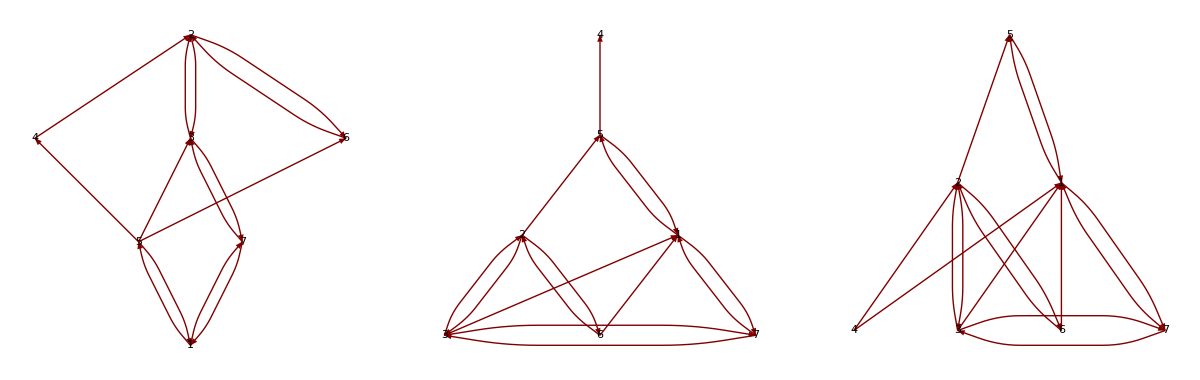

```mathematica
GraphicsRow[{fig1,fig2,fig3},ImageSize->Full]
```

## Example 4

```mathematica
d=goodSemiCompleteD[8,2]
```

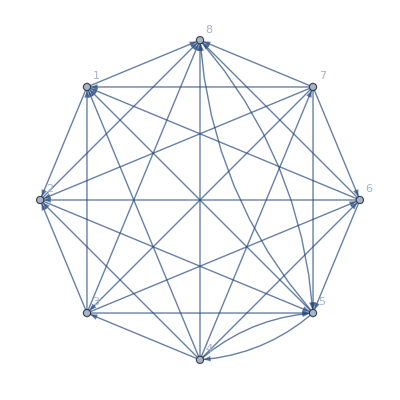
```mathematica
d=-Graphics-
```

-Graphics-

```mathematica
bfsVPartition[d,#]&/@maxOutDegreeVS@d
```

{{{{4},{}},{{5},{}},{{7,3,6,2,8},{}},{{1},{}}}}

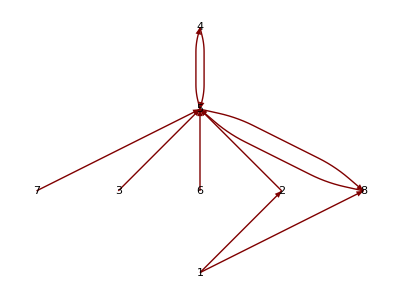

```mathematica
fig1=LayeredGraphPlot[{4->5,5->4,7->5,3->5,6->5,2->5,5->8,8->5,1->2,1->8},VertexLabeling->True,MultiedgeStyle->All,VertexCoordinateRules->{{0,3},{0,2},{-2,1},{-1,1},{0,1},{1,1},{2,1},{0,0}}]
```

```mathematica
CyclePacking={{4,5}};
```

```mathematica
FeedbackVS={5};
```

```mathematica
d//AcyclicGraphQ[Subgraph[#,Complement[VertexList[#],FeedbackVS]]]&
```

True

## Example 5(?)

What if we require the digraph is 2-connected? Or the order for vertices in 2-cycles depends on the least vertex in this 2-cycle?

```mathematica
d=goodSemiCompleteD[9,3]
```

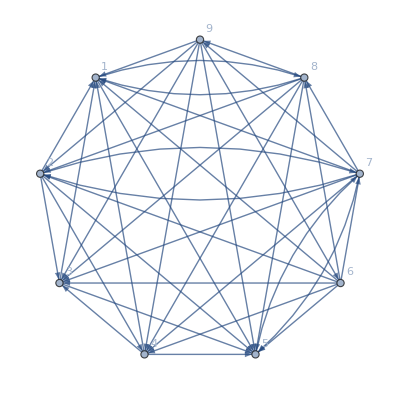
```mathematica
d=-Graphics-
```

-Graphics-

```mathematica
bfsVPartition[d,#]&/@maxOutDegreeVS@d
```

{{{{6},{}},{{9},{}},{{7,8},{}},{{2,1,5},{}},{{4,3},{}}},{{{7},{}},{{6,2,5},{}},{{1,3,4,8,9},{{1->8,8->1},{1->8,8->9,9->1},{1->8,8->4,4->1},{1->8,8->3,3->1}}}}}

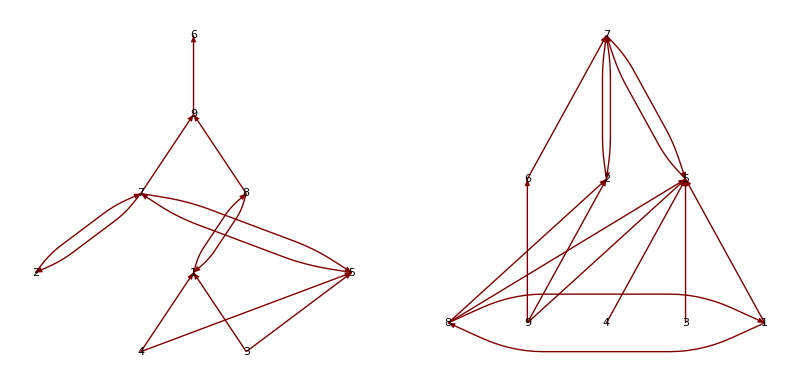

```mathematica
fig1=LayeredGraphPlot[{9->6,7->9,8->9,2->7,7->2,1->8,8->1,5->7,7->5,4->1,4->5,3->1,3->5},VertexLabeling->True,MultiedgeStyle->All,VertexCoordinateRules->{{0,3},{0,4},{-0.5,2},{0.5,2},{-1.5,1},{0,1},{1.5,1},{-0.5,0},{0.5,0}}];
fig2=LayeredGraphPlot[{6->7,7->2,2->7,5->7,7->5,8->2,8->5,9->6,9->2,9->5,4->5,3->5,1->5,8->1,1->8},VertexLabeling->True,MultiedgeStyle->All,VertexCoordinateRules->{{-1,1},{0,2},{0,1},{1,1},{-2,0},{-1,0},{0,0},{1,0},{2,0}}];
GraphicsRow[{fig1,fig2},ImageSize->Full]
```

```mathematica
CyclePacking={{{6,7,9},{1,8}},{{2,7},{1,8}}};
```

```mathematica
FeedbackVS={7,8};
```

```mathematica
d//AcyclicGraphQ[Subgraph[#,Complement[VertexList[#],FeedbackVS]]]&
```

True

## Example 6(bad one)

This digraph contains a 5-ring, which can be obtained by contracting vertex 3 in 3-cycle {1,3,6}

```mathematica
goodSemiCompleteD[9,6]
```

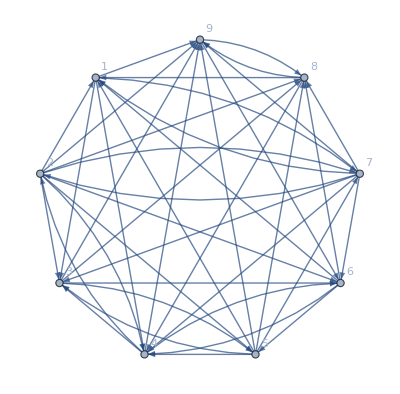
```mathematica
d=-Graphics-
```

-Graphics-

```mathematica
bfsVPartition[d,#]&/@maxOutDegreeVS@d
```

{{{{2},{}},{{7,4},{}},{{6,5,8,1},{}},{{3,9},{}}}}

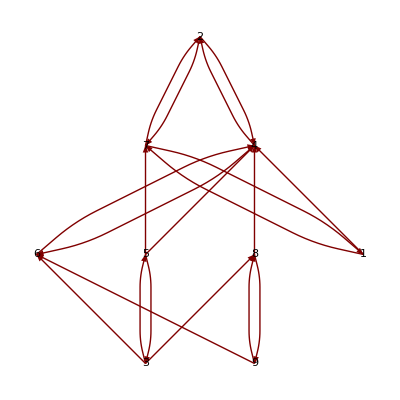

```mathematica
fig1=LayeredGraphPlot[{2->7,7->2,2->4,4->2,4->6,6->4,5->7,5->4,8->4,1->7,7->1,1->4,3->6,3->5,5->3,3->8,9->6,8->9,9->8},VertexLabeling->True,MultiedgeStyle->All,VertexCoordinateRules->{{0.5,3},{0,2},{1,2},{-1,1},{0,1},{1,1},{2,1},{0,0},{1,0}}]
```

```mathematica
CyclePacking={{2,7},{4,6},{3,5},{8,9}};
```

```mathematica
FeedbackVS={4,7,3,9};
```

```mathematica
d//AcyclicGraphQ[Subgraph[#,Complement[VertexList[#],FeedbackVS]]]&
```

True

## Example 7

```mathematica
goodSemiCompleteD[8,8]
```

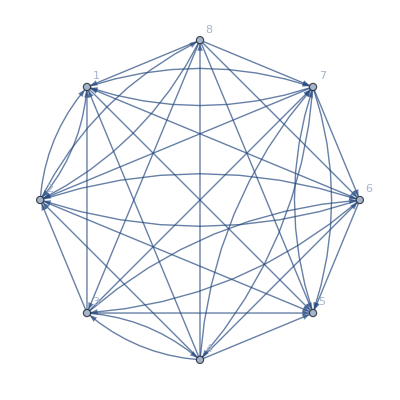
```mathematica
d=-Graphics-
```

-Graphics-

```mathematica
bfsVPartition[d,#]&/@maxOutDegreeVS@d
```

{{{{4},{}},{{3,7},{}},{{8,6,1,5},{}},{{2},{}}}}

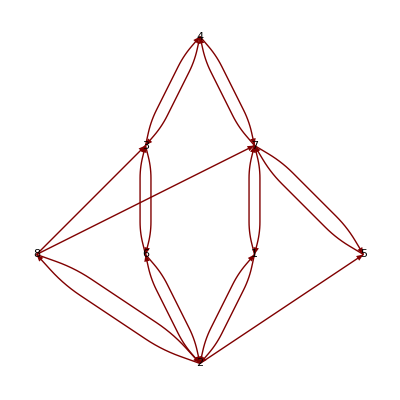

```mathematica
fig1=LayeredGraphPlot[{4->3,3->4,4->7,7->4,8->3,3->6,6->3,1->7,7->1,5->7,7->5,2->8,8->2,2->6,6->2,2->1,1->2,2->5,8->7},VertexLabeling->True,MultiedgeStyle->All,VertexCoordinateRules->{{1.5,2},{1,1},{2,1},{0,0},{1,0},{2,0},{3,0},{1.5,-1}}]
```

```mathematica
CyclePacking={{3,4},{1,7},{2,8}};
```

```mathematica
FeedbackVS={2,3,7};
```

```mathematica
d//AcyclicGraphQ[Subgraph[#,Complement[VertexList[#],FeedbackVS]]]&
```

True

## Example 8

```mathematica
goodSemiCompleteD[6,10]
```

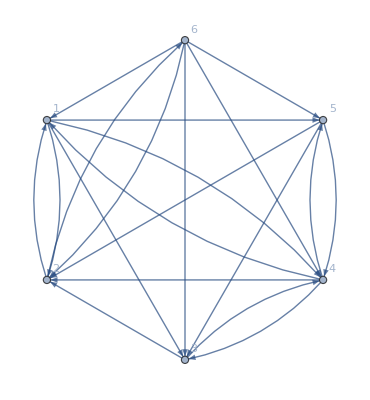
```mathematica
d=-Graphics-
```

-Graphics-

```mathematica
bfsVPartition[d,#]&/@maxOutDegreeVS@d
```

{{{{6},{}},{{2},{}},{{1,3,4,5},{{4->5,5->4},{3->4,4->3},{1->4,4->1},{3->4,4->5,5->3},{1->5,5->4,4->1},{1->3,3->4,4->1}}}}}

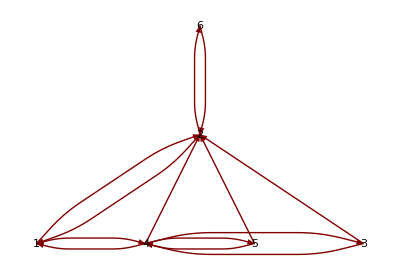

```mathematica
fig1=LayeredGraphPlot[{6->2,2->6,1->2,2->1,4->2,5->2,3->2,1->4,4->1,4->5,5->4,3->4,4->3},VertexLabeling->True,MultiedgeStyle->All,VertexCoordinateRules->{{1.5,2},{1.5,1},{0,0},{1,0},{2,0},{3,0}}]
```

```mathematica
CyclePacking={{2,6},{3,4}};
```

```mathematica
FeedbackVS={2,4};
```

```mathematica
d//AcyclicGraphQ[Subgraph[#,Complement[VertexList[#],FeedbackVS]]]&
```

True

## Example 9

```mathematica
goodSemiCompleteD[7,12]
```

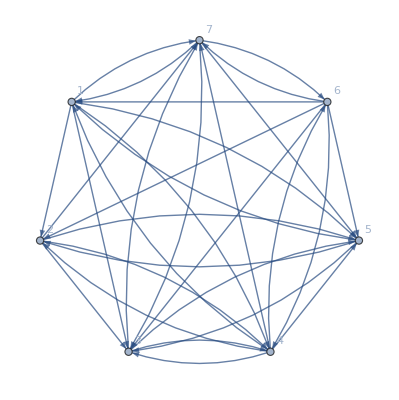
```mathematica
d=-Graphics-
```

-Graphics-

```mathematica
bfsVPartition[d,#]&/@maxOutDegreeVS@d
```

{{{{4},{}},{{6,1,2,3},{}},{{7,5},{}}},{{{6},{}},{{4,7},{}},{{1,2,3},{}},{{5},{}}}}

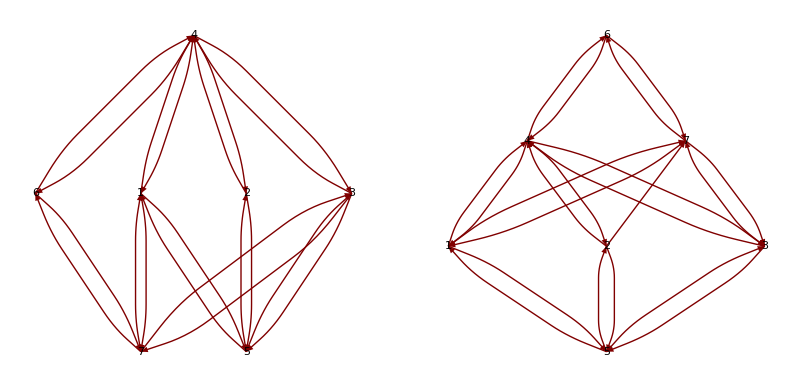

```mathematica
fig1=LayeredGraphPlot[{4->6,6->4,1->4,4->1,2->4,4->2,3->4,4->3,6->7,7->6,1->7,7->1,3->7,7->3,1->5,5->1,2->5,5->2,3->5,5->3},VertexLabeling->True,MultiedgeStyle->All,VertexCoordinateRules->{{1.5,2},{0,1},{1,1},{2,1},{3,1},{1,0},{2,0}}];
fig2=LayeredGraphPlot[{4->6,6->4,1->4,4->1,2->4,4->2,3->4,4->3,6->7,7->6,1->7,7->1,3->7,7->3,1->5,5->1,2->5,5->2,3->5,5->3,2->7},VertexLabeling->True,MultiedgeStyle->All,VertexCoordinateRules->{{0.5,2},{1,3},{0,1},{1,1},{2,1},{1.5,2},{1,0}}];
GraphicsRow[{fig1,fig2},ImageSize->Full]
```

```mathematica
CyclePacking={{4,6},{1,7},{2,5}};
```

```mathematica
FeedbackVS={4,5,7};
```

```mathematica
d//AcyclicGraphQ[Subgraph[#,Complement[VertexList[#],FeedbackVS]]]&
```

True

```mathematica
goodSemiCompleteD[8,6]
```

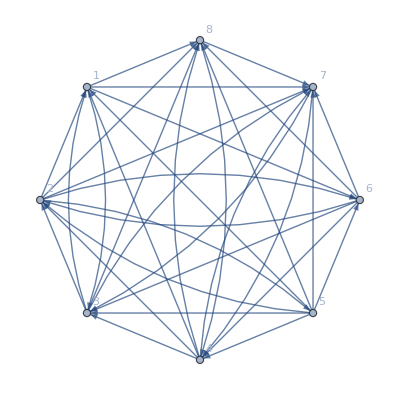
```mathematica
d=-Graphics-
```

-Graphics-

```mathematica
bfsVPartition[d,#]&/@maxOutDegreeVS@d
```

{{{{5},{}},{{2},{}},{{6,4,3},{}},{{1,8,7},{}}}}

```mathematica
goodSemiCompleteD[7,10]
```

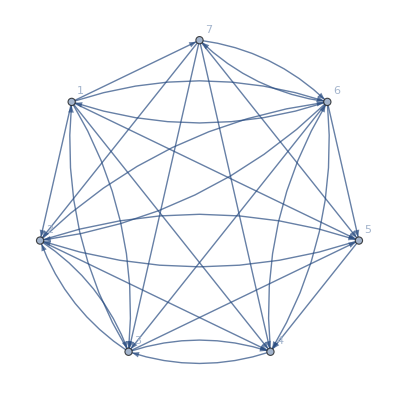
```mathematica
d=-Graphics-
```

-Graphics-

```mathematica
bfsVPartition[d,#]&/@maxOutDegreeVS@d
```

{{{{1},{}},{{6,3},{}},{{7,2,4},{}},{{5},{}}},{{{6},{}},{{1,7,2,4},{}},{{3,5},{}}}}

```mathematica
goodSemiCompleteD[9,5]
```

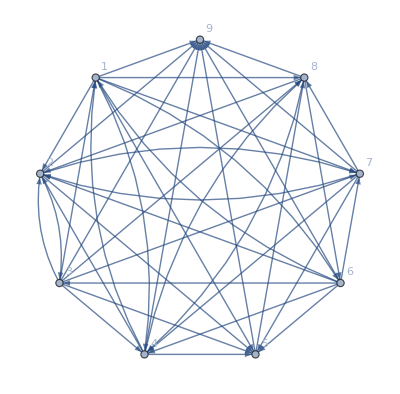
```mathematica
d=-Graphics-
```

-Graphics-

```mathematica
bfsVPartition[d,#]&/@maxOutDegreeVS@d
```

$Aborted

```mathematica
VertexOutDegree[d]
```

{7,4,7,5,2,7,5,4,0}

```mathematica
VertexOutComponent[d,1,1]
```

{1,2,5,6,7,8,9,4}

```mathematica
goodSemiCompleteD[10,5]
```

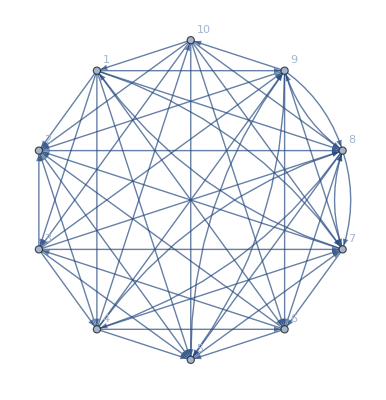
```mathematica
d=-Graphics-
```

-Graphics-

```mathematica
bfsVPartition[d,#]&/@maxOutDegreeVS@d
```

{{{{1},{}},{{10,7},{}},{{3,4,5,8,9},{{8->9,9->8},{5->9,9->5},{4->8,8->4},{5->9,9->8,8->5},{4->9,9->8,8->4}}},{{6,2},{}}}}

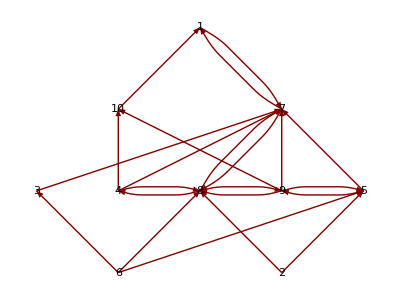

```mathematica
fig1=LayeredGraphPlot[{10->1,1->7,7->1,3->7,4->10,4->7,8->7,7->8,9->10,9->7,5->7,4->8,8->4,8->9,9->8,9->5,5->9,6->3,6->8,6->5,2->8,2->5},VertexLabeling->True,MultiedgeStyle->All,VertexCoordinateRules->{{1,2},{2,3},{3,2},{0,1},{1,1},{2,1},{3,1},{4,1},{1,0},{3,0}}]
```

```mathematica
CyclePacking={{1,7},{4,8},{5,9}};
```

```mathematica
FeedbackVS={4,7,9};
```

```mathematica
d//AcyclicGraphQ[Subgraph[#,Complement[VertexList[#],FeedbackVS]]]&
```

True

## Example (Bad one)

Contracting vertex 1 and vertex 5 yields a 5- ring consisting of {3,7,2,9,6},f

```mathematica
goodSemiCompleteD[10,4]
```

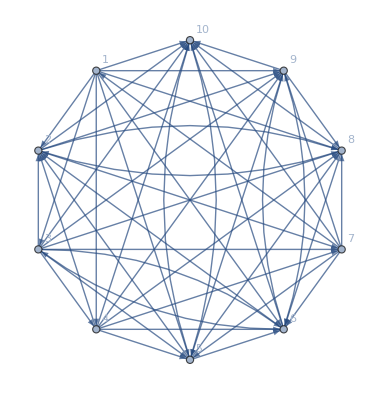
```mathematica
d=-Graphics-
```

-Graphics-

```mathematica
bfsVPartition[d,#]&/@maxOutDegreeVS@d
```

{{{{1},{}},{{7},{}},{{3,4,2},{}},{{5,8,6},{}},{{9,10},{}}},{{{3},{}},{{1,6},{}},{{4,7,9,5,8},{}},{{2,10},{}}}}

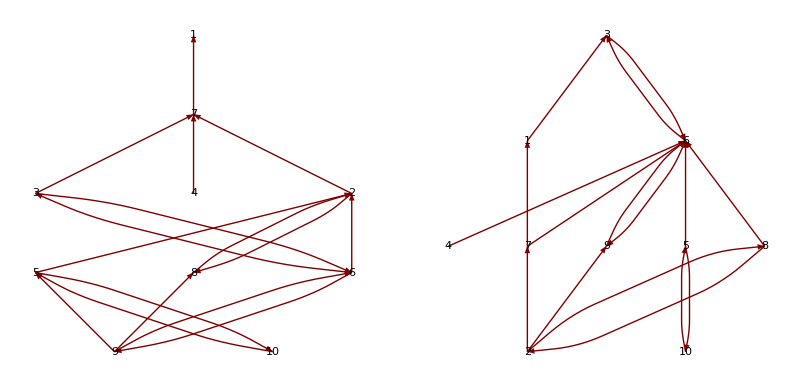

```mathematica
fig1=LayeredGraphPlot[{7->1,3->7,4->7,2->7,5->2,8->2,2->8,3->6,6->3,6->2,9->5,9->8,9->6,6->9,10->5,5->10},VertexLabeling->True,MultiedgeStyle->All,VertexCoordinateRules->{{1,4},{1,5},{0,3},{1,3},{2,3},{0,2},{1,2},{2,2},{0.5,1},{1.5,1}}];
fig2=LayeredGraphPlot[{1->3,3->6,6->3,4->6,7->1,7->6,9->6,6->9,5->6,8->6,2->7,2->9,2->8,8->2,10->5,5->10},VertexLabeling->True,MultiedgeStyle->All,VertexCoordinateRules->{{1,2},{2,3},{3,2},{0,1},{1,1},{2,1},{3,1},{4,1},{1,0},{3,0}}];
GraphicsRow[{fig1,fig2},ImageSize->Full]
```

```mathematica
goodSemiCompleteD[8,3]
```

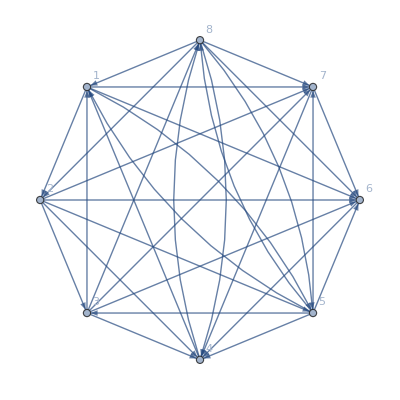
```mathematica
d=-Graphics-
```

-Graphics-

```mathematica
bfsVPartition[d,#]&/@maxOutDegreeVS@d
```

{{{{5},{}},{{8,1,2},{}},{{3,4},{}},{{7,6},{}}},{{{8},{}},{{5,3,4},{}},{{1,2,7,6},{}}}}

```mathematica
goodSemiCompleteD[9,3]
```

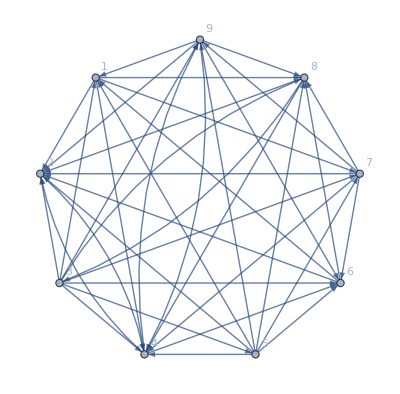
```mathematica
d=-Graphics-
```

-Graphics-

```mathematica
bfsVPartition[d,#]&/@maxOutDegreeVS@d
```

{{{{3},{}},{{8},{}},{{1,5,6,7,9},{{1->7,7->9,9->1},{1->7,7->6,6->1}}},{{4},{}},{{2},{}}}}

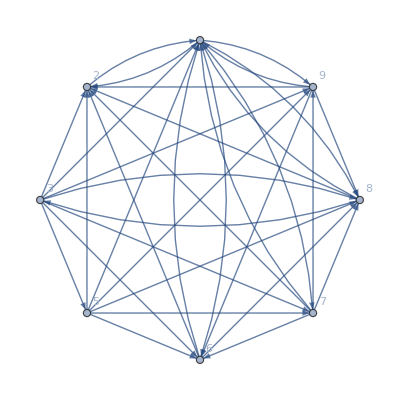

```mathematica
EdgeContract[d,{1->4}]
```

```mathematica
IncidenceMatrix[%21]
```

SparseArray[<68>, {8, 34}]

```mathematica
IncidenceMatrix[%52]
```

SparseArray[<64>, {8, 32}]

```mathematica
IncidenceMatrix[%46]
```

SparseArray[<66>, {8, 33}]

```mathematica
t=IncidenceGraph@IncidenceMatrix[%52];
```

```mathematica
IncidenceMatrix[%22]
```

SparseArray[<66>, {8, 33}]

```mathematica
t=IncidenceGraph[IncidenceMatrix[%21]]
```

-Graphics-

```mathematica
t2=EdgeContract[t,]
```

```mathematica
goodQ[d_]:=Module[{dsubgraphs,f1,f11,f12,f2,f3,f41,f42,f421,f422,f43,f51,f52,f521,f522,f523,f524,f53,f531,f532,f533,f534,f54,residularcsf54,f54all,dforbiddens},
		dsubgraphs=Subgraph[d,#]&/@Subsets[VertexList@d,{3,Min[VertexCount@d,5]}];
		f1=Graph[{1->4,4->3,3->2,2->1,2->5,4->5,5->1,5->3}];
		f11=EdgeAdd[f1,{1->3,2->4}];
		f12=EdgeAdd[f1,{1->3,4->2}];
		f2=Graph[{1->2,2->3,3->4,4->5,5->1,2->5,3->1,4->2,5->3,1->4}];
		f3=Graph[{1->2,2->1,2->3,3->2,3->1,1->3}]; (*3-Ring*)
		f41=Graph[{1->2,2->3,3->2,1->3,2->4,3->4,4->1}]; (*K4 with one C2*)
		f42=Graph[{1->2,2->4,4->1,2->3,3->2,3->4,4->3}]; (*K4 with two C2, two cases*)
		f421=EdgeAdd[f42,{1->3}];
		f422=EdgeAdd[f42,{3->1}];
		f43=Graph[{1->2,2->3,3->1,1->4,4->1,2->4,4->2,3->4,4->3}]; (*K4 with three C2, 3-wheel W3*)
		f51=Graph[{1->2,2->3,3->4,4->5,5->1,4->3,1->4,3->1,4->2,5->2,5->3}]; (*K5 with one C2, case 1*)
		f52=Graph[{1->2,2->3,3->1,1->5,5->4,4->1,3->4,4->3}];
		f521=EdgeAdd[f52,{2->5,2->4,3->5}];
		f522=EdgeAdd[f52,{2->5,4->2,3->5}];
		f523=EdgeAdd[f52,{5->2,2->4,3->5}];
		f524=EdgeAdd[f52,{2->5,2->4,5->3}];
		f53=Graph[{1->3,3->2,2->1,1->4,4->5,5->1,3->4,4->3}];
		f531=EdgeAdd[f52,{2->5,2->4,3->5}];
		f532=EdgeAdd[f52,{2->5,4->2,3->5}];
		f533=EdgeAdd[f52,{5->2,2->4,3->5}];
		f534=EdgeAdd[f52,{2->5,2->4,5->3}];
		f54=Graph[{1->2,2->1,2->3,3->2,3->4,4->3,4->5,5->4,5->1,1->5}]; (*5-Ring*)
		residularcsf54={{DirectedEdge[1,3],DirectedEdge[3,1]},{DirectedEdge[1,4],DirectedEdge[4,1]},{DirectedEdge[2,4],DirectedEdge[4,2]},{DirectedEdge[2,5],DirectedEdge[5,2]},{DirectedEdge[3,5],DirectedEdge[5,3]}};
		f54all=EdgeAdd[f54,#]&/@Tuples[residularcsf54];
	dforbiddens={f11,f12,f2,f3,f41,f421,f422,f43,f51,f521,f522,f523,f524,f531,f532,f533,f534}∪f54all;
		SameQ[Or@@Flatten@Outer[IsomorphicGraphQ,dsubgraphs,dforbiddens],False]];
```

```mathematica
goodQ[t]
```

True

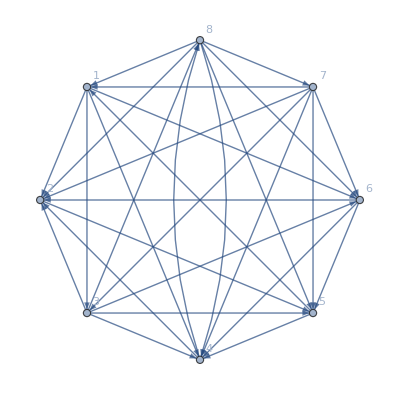

```mathematica
d=goodSemiCompleteD[8]
```

```mathematica
bfsVPartition[d,#]&/@maxOutDegreeVS@d
```

{{{{7},{}},{{8},{}},{{3,4},{}},{{1,5,6},{{1->6,6->5,5->1}}},{{2},{}}},{{{8},{}},{{3,4},{}},{{1,5,6,7},{{1->6,6->5,5->1}}},{{2},{}}}}

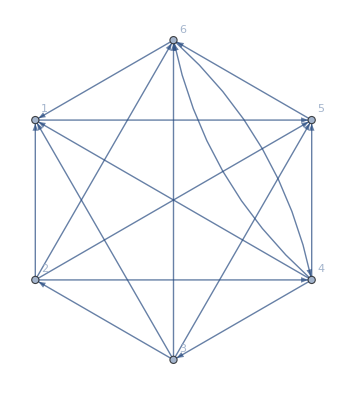

```mathematica
d=goodSemiCompleteD[6]
```

```mathematica
bfsVPartition[d,#]&/@maxOutDegreeVS@d
```

{{{{2},{}},{{3},{}},{{4},{}},{{6},{}},{{5},{}},{{1},{}}},{{{3},{}},{{4},{}},{{2,6},{}},{{5},{}},{{1},{}}},{{{4},{}},{{2,6},{}},{{3,5},{}},{{1},{}}}}

```mathematica
d=goodSemiCompleteD[6];bfsVPartition[d,#]&/@maxOutDegreeVS@d
```

{{{{3},{}},{{5,1},{}},{{4},{}},{{2},{}},{{6},{}}},{{{5},{}},{{3,4},{}},{{1,2},{}},{{6},{}}}}

```mathematica
d=goodSemiCompleteD[6];bfsVPartition[d,#]&/@maxOutDegreeVS@d
```

{{{{4},{}},{{5},{}},{{1,2,3},{}},{{6},{}}}}

```mathematica
d=goodSemiCompleteD[6];bfsVPartition[d,#]&/@maxOutDegreeVS@d
```

{{{{2},{}},{{5},{}},{{4},{}},{{6,1,3},{}}},{{{5},{}},{{4},{}},{{2,6,1,3},{}}}}

```mathematica
d=goodSemiCompleteD[6];bfsVPartition[d,#]&/@maxOutDegreeVS@d
```

{{{{1},{}},{{6},{}},{{4,2},{}},{{5},{}},{{3},{}}}}

```mathematica
Do[d=goodSemiCompleteD[6];Print@bfsVPartition[d,#]&/@maxOutDegreeVS@d,{10}]
```

{{{1},{}},{{3},{}},{{4,2},{}},{{5,6},{}}}

{{{4},{}},{{6},{}},{{2},{}},{{3,5},{}},{{1},{}}}

{{{6},{}},{{2},{}},{{4,3,5},{}},{{1},{}}}

{{{2},{}},{{5},{}},{{3,6,4},{}},{{1},{}}}

{{{3},{}},{{2},{}},{{5},{}},{{6,4},{}},{{1},{}}}

{{{5},{}},{{3},{}},{{6,1},{}},{{4},{}},{{2},{}}}

{{{6},{}},{{5},{}},{{3},{}},{{1},{}},{{4},{}},{{2},{}}}

{{{3},{}},{{4},{}},{{6,2},{}},{{1,5},{}}}

$Aborted

```mathematica
Do[d=goodSemiCompleteD[6];Print@d;Print@bfsVPartition[d,#]&/@maxOutDegreeVS@d,{10}]
```

{{{1},{}},{{2,6},{}},{{5,4,3},{}}}

{{{5},{}},{{2,6},{}},{{4,3,1},{}}}

{{{2},{}},{{3},{}},{{4,1},{}},{{5,6},{}}}

{{{1},{}},{{2},{}},{{3,4,5,6},{{4->6,6->5,5->4},{3->4,4->6,6->3}}}}

{{{1},{}},{{5},{}},{{6,3,4,2},{}}}

{{{6},{}},{{1},{}},{{5},{}},{{3,4,2},{}}}

{{{3},{}},{{5},{}},{{4,1,2},{}},{{6},{}}}

{{{4},{}},{{5,3},{}},{{1,2},{}},{{6},{}}}

$Aborted

{{{6},{}},{{4,1},{}},{{3,5,2},{}}}

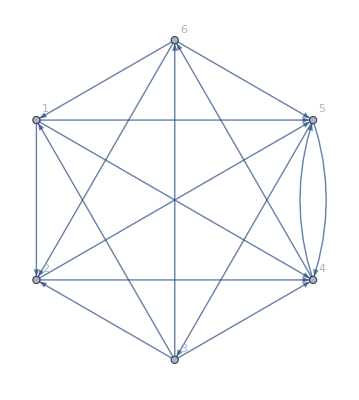

{{{3},{}},{{5},{}},{{1,2,4,6},{{2->4,4->6,6->2},{1->4,4->6,6->1}}}}

```mathematica
Do[d=goodSemiCompleteD[6];Print@d;Print@bfsVPartition[d,#]&/@maxOutDegreeVS@d,{10}]
```

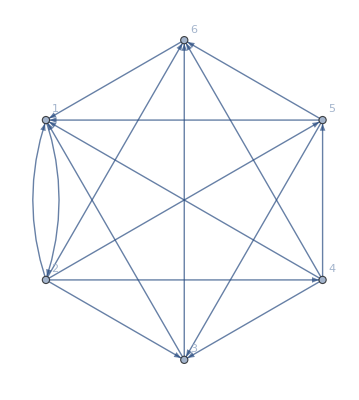

{{{2},{}},{{1},{}},{{4,5,3,6},{}}}

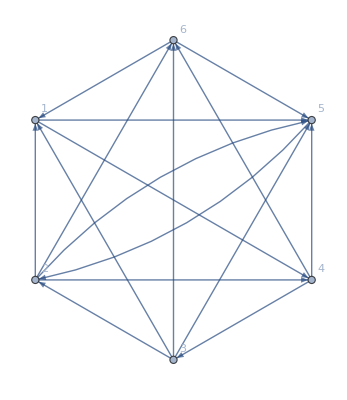
d=-Graphics-

{{{2},{}},{{3,5},{}},{{1,4,6},{{1->4,4->6,6->1}}}}

{{{3},{}},{{4},{}},{{2,1},{}},{{6,5},{}}}

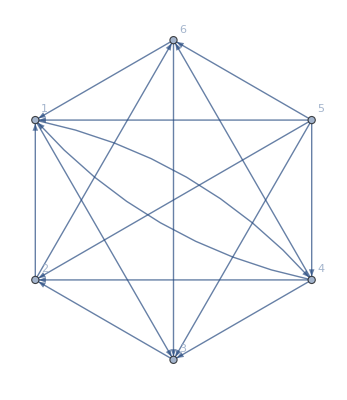

$Aborted

```mathematica
Do[d=goodSemiCompleteD[6];Print@d;Print@bfsVPartition[d,#]&/@maxOutDegreeVS@d,{10}]
```

```mathematica
d=-Graphics-
```

-Graphics-

```mathematica
bfsVPartition[d,#]&/@maxOutDegreeVS@d
```

{{{{2},{}},{{3,5},{}},{{1,4,6},{{1->4,4->6,6->1}}}},{{{3},{}},{{4},{}},{{2,1},{}},{{6,5},{}}}}

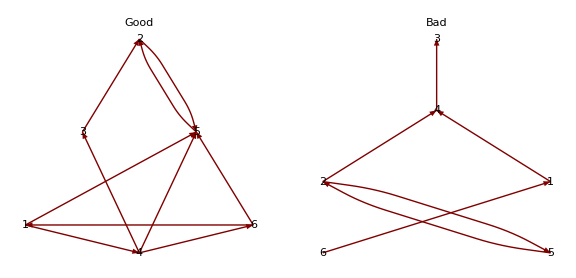

```mathematica
fig1=LayeredGraphPlot[{3->2,2->5,5->2,1->5,4->3,4->5,6->5,1->4,4->6,6->1},VertexLabeling->True,MultiedgeStyle->All,VertexCoordinateRules->{{0.5,1},{1,2},{1.5,1},{0,0},{1,-0.3},{2,0}},PlotLabel->"Good"];
fig2=LayeredGraphPlot[{4->3,2->4,1->4,6->1,5->2,2->5},VertexLabeling->True,MultiedgeStyle->All,VertexCoordinateRules->{{1,2},{1,3},{0,1},{2,1},{0,0},{2,0}},PlotLabel->"Bad"];
GraphicsRow[{fig1,fig2},ImageSize->Large]
```

```mathematica
FeedbackVS={1,2};
```

```mathematica
d//AcyclicGraphQ[Subgraph[#,Complement[VertexList[#],FeedbackVS]]]&
```

True

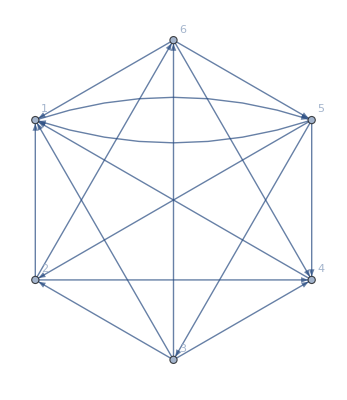
```mathematica
d=-Graphics-
```

-Graphics-

```mathematica
FeedbackVS={5};
```

```mathematica
d//AcyclicGraphQ[Subgraph[#,Complement[VertexList[#],FeedbackVS]]]&
```

True

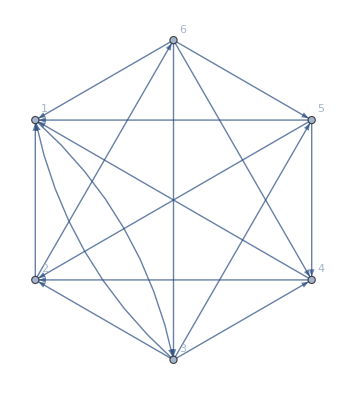
```mathematica
d=-Graphics-
```

-Graphics-

```mathematica
bfsVPartition[d,#]&/@maxOutDegreeVS@d
```

{{{{3},{}},{{6,1},{}},{{5,4,2},{}}},{{{6},{}},{{2},{}},{{3,5,4},{}},{{1},{}}}}

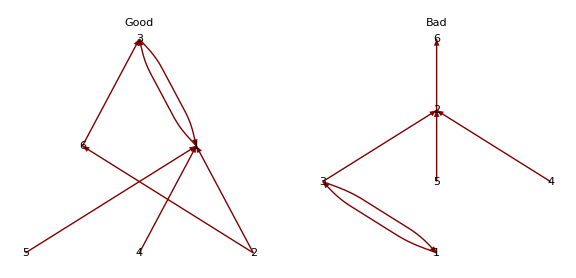

```mathematica
fig1=LayeredGraphPlot[{6->3,1->3,3->1,5->1,4->1,2->6,2->1},VertexLabeling->True,MultiedgeStyle->All,VertexCoordinateRules->{{0.5,1},{1,2},{1.5,1},{0,0},{1,0},{2,0}},PlotLabel->"Good"];
fig2=LayeredGraphPlot[{2->6,3->2,5->2,4->2,1->3,3->1},VertexLabeling->True,MultiedgeStyle->All,VertexCoordinateRules->{{1,2},{1,3},{0,1},{1,1},{2,1},{1,0}},PlotLabel->"Bad"];
GraphicsRow[{fig1,fig2},ImageSize->Large]
```

```mathematica
FeedbackVS={1,6};
```

```mathematica
d//AcyclicGraphQ[Subgraph[#,Complement[VertexList[#],FeedbackVS]]]&
```

True

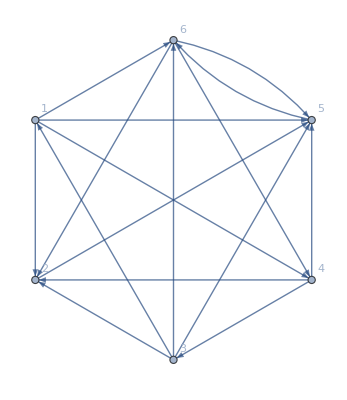
```mathematica
d=-Graphics-
```

-Graphics-

```mathematica
bfsVPartition[d,#]&/@maxOutDegreeVS@d
```

{{{{1},{}},{{3},{}},{{4},{}},{{6},{}},{{5},{}},{{2},{}}},{{{3},{}},{{4},{}},{{1,6},{}},{{5},{}},{{2},{}}}}

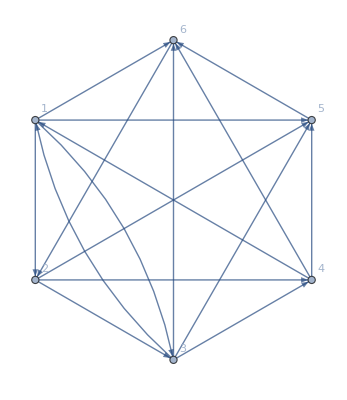
```mathematica
d=-Graphics-
```

-Graphics-

```mathematica
bfsVPartition[d,#]&/@maxOutDegreeVS@d
```

{{{{1},{}},{{3,4},{}},{{2},{}},{{6},{}},{{5},{}}},{{{3},{}},{{1,2},{}},{{4,6},{}},{{5},{}}}}

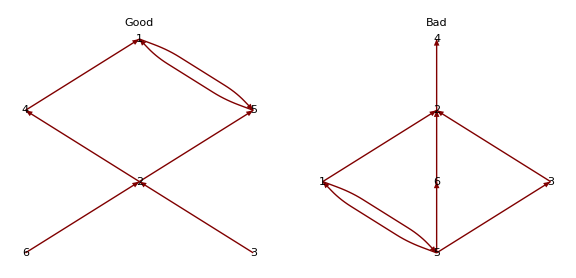

```mathematica
fig1=LayeredGraphPlot[{4->1,5->1,1->5,2->4,2->5,6->2,3->2},VertexLabeling->True,MultiedgeStyle->All,VertexCoordinateRules->{{0,2},{1,3},{2,2},{1,1},{0,0},{2,0}},PlotLabel->"Good"];
fig2=LayeredGraphPlot[{2->4,1->2,6->2,3->2,5->1,1->5,5->6,5->3},VertexLabeling->True,MultiedgeStyle->All,VertexCoordinateRules->{{1,2},{1,3},{0,1},{1,1},{2,1},{1,0}},PlotLabel->"Bad"];
GraphicsRow[{fig1,fig2},ImageSize->Large]
```

```mathematica
FeedbackVS={1,2};
```

```mathematica
d//AcyclicGraphQ[Subgraph[#,Complement[VertexList[#],FeedbackVS]]]&
```

True

```mathematica
d=-Graphics-
```

-Graphics-

```mathematica
bfsVPartition[d,#]&/@maxOutDegreeVS@d
```

{{{{3},{}},{{5},{}},{{1,2,4,6},{{2->4,4->6,6->2},{1->4,4->6,6->1}}}}}

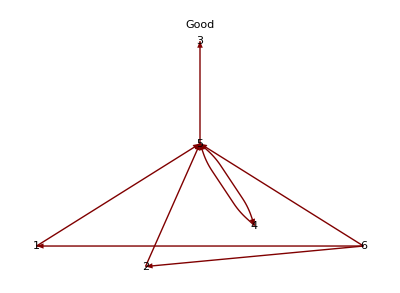

```mathematica
fig=LayeredGraphPlot[{5->3,1->5,2->5,4->5,5->4,6->5,6->1,6->2},VertexLabeling->True,MultiedgeStyle->All,VertexCoordinateRules->{{1.5,1},{1.5,2},{0,0},{1,-0.2},{2,0.2},{3,0}},PlotLabel->"Good"]
```

```mathematica
FeedbackVS={3,4};
```

```mathematica
d//AcyclicGraphQ[Subgraph[#,Complement[VertexList[#],FeedbackVS]]]&
```

True

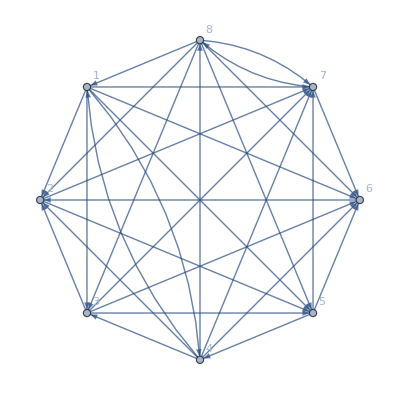

{{{1},{}},{{4,8},{}},{{5,7},{}},{{3,2},{}},{{6},{}}}

{{{4},{}},{{1,5},{}},{{8,3,2},{}},{{7,6},{}}}

{{{8},{}},{{4,7},{}},{{1,3,2,5},{}},{{6},{}}}

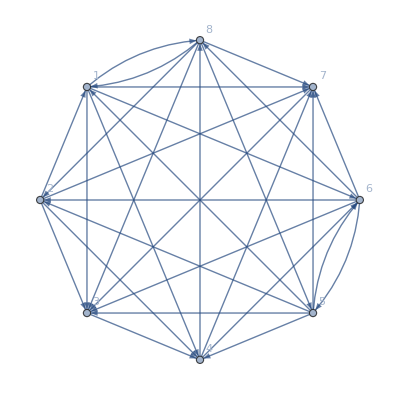

{{{5},{}},{{6,8},{}},{{1,4},{}},{{2,3},{}},{{7},{}}}

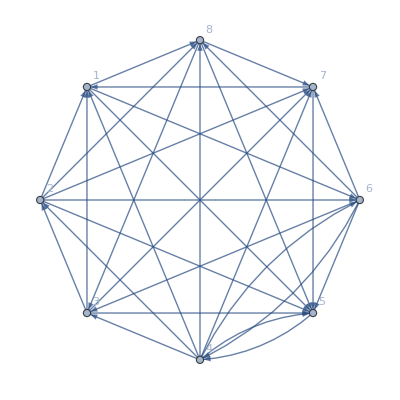

{{{4},{}},{{6,5},{}},{{1,2,3,7,8},{{2->8,8->3,3->2},{1->8,8->7,7->1},{1->8,8->3,3->1}}}}

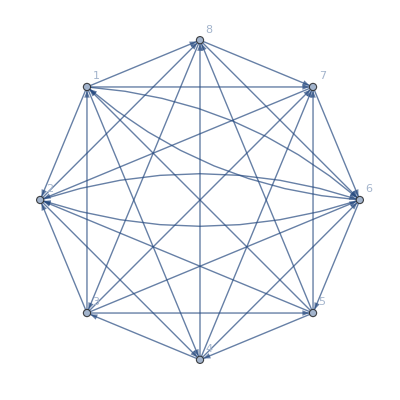

{{{1},{}},{{3,6,5},{}},{{2,4,7,8},{{2->8,8->7,7->2},{2->4,4->7,7->2}}}}

{{{3},{}},{{4,8},{}},{{5,1,2},{}},{{7,6},{}}}

{{{5},{}},{{3,6},{}},{{1,2,4,7,8},{{2->8,8->7,7->2},{2->4,4->7,7->2}}}}

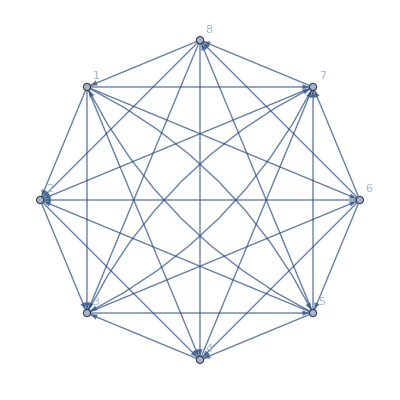

{{{1},{}},{{5,8},{}},{{3,6,7},{{3->7,7->3},{3->6,6->7,7->3}}},{{2,4},{}}}

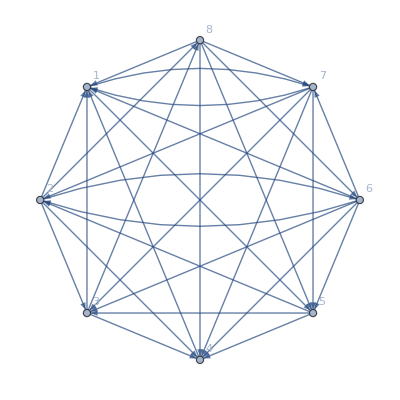

{{{6},{}},{{2,8},{}},{{7,5,3},{}},{{1},{}},{{4},{}}}

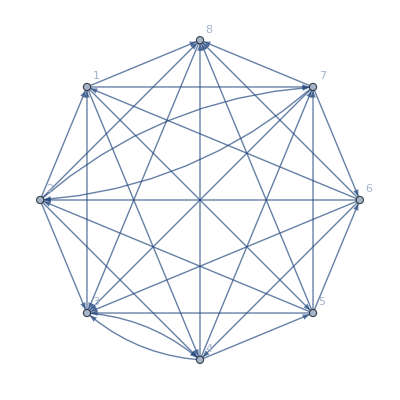

{{{2},{}},{{5,7,6},{}},{{1,4},{}},{{3},{}},{{8},{}}}

{{{5},{}},{{1,4},{}},{{6,2,3},{}},{{7,8},{}}}

{{{6},{}},{{5,7},{}},{{2,1,4},{}},{{3},{}},{{8},{}}}

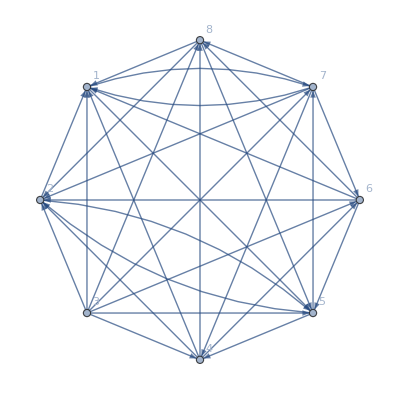

$Aborted

```mathematica
Do[d=goodSemiCompleteD[8,2];Print@d;Print@bfsVPartition[d,#]&/@maxOutDegreeVS@d,{10}]
```